{9.62,9.9,4.25,11.51,13.45,12.47,18.26,4.98,12.46,13.62,14.74,4.08,11.17,9.11,9.58,17.2,8.42,15.46,9.91,12.59,11.73,1.2,15.12,13.08,17.32,13.84,20.76,11.95,12.47,13.02,19.05,13.41,16.91,13.2,13.13,11.78,14.23,19.1,1.7,14.27,13.62,12.19,16.57,0.83,9.73,16.59,15.78,12.26,13.93,10.94,15.15,10.25,14.26,13.79,15.82,11.11,15.,12.85,11.4,13.36,17.54,9.78,15.05,9.16,15.97,4.46,14.27,20.18,11.91,13.18,10.78,15.,11.73,9.16,12.2,13.76,14.71,0.25,8.01,16.93,12.56,9.81,11.53,10.19,17.3,13.41,14.87,13.21,12.95,10.65,9.25,8.89,14.89,18.84,13.45,11.95,10.95,18.67,4.36,10.22}

4.645

Q1: 10.235

Q2 (Median): 12.9

Q3: 14.88

Inner Fences: {3.2675,21.8475}

Actual Whisker Ends: {20.76,0.25}

Outer Fences: {-3.7,28.815}

Near Outliers: {0.25,0.83,1.2,1.7}

Far Outliers: {}

28.815

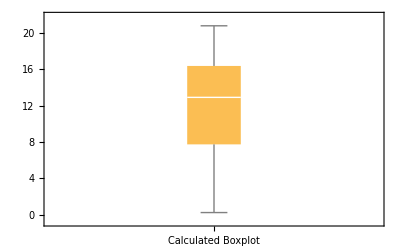

```mathematica
data={9.62,9.90,4.25,11.51,13.45,12.47,18.26,4.98,12.46,13.62,14.74,4.08,11.17,9.11,9.58,17.20,8.42,15.46,9.91,12.59,11.73,1.20,15.12,13.08,17.32,13.84,20.76,11.95,12.47,13.02,19.05,13.41,16.91,13.2,13.13,11.78,14.23,19.10,1.70,14.27,13.62,12.19,16.57,0.83,9.73,16.59,15.78,12.26,13.93,10.94,15.15,10.25,14.26,13.79,15.82,11.11,15.00,12.85,11.40,13.36,17.54,9.78,15.05,9.16,15.97,4.46,14.27,20.18,11.91,13.18,10.78,15.00,11.73,9.16,12.20,13.76,14.71,0.25,8.01,16.93,12.56,9.81,11.53,10.19,17.30,13.41,14.87,13.21,12.95,10.65,9.25,8.89,14.89,18.84,13.45,11.95,10.95,18.67,4.36,10.22}

(*Sort the data (important for accurate quartile calculation)*)
sortedData=Sort[data];

(*Calculate quartiles using Quartiles*)
quartiles=Quartiles[sortedData];
q1=quartiles[[1]];
q2=quartiles[[2]];
q3=quartiles[[3]];


(*Calculate IQR (Interquartile Range)*)
iqr=q3-q1

(*Calculate Inner Fences*)
innerLowerFence=q1-1.5*iqr;
innerUpperFence=q3+1.5*iqr;
innerFences={innerLowerFence,innerUpperFence};

(*Calculate Outer Fences*)
outerLowerFence=q1-3*iqr;
outerUpperFence=q3+3*iqr;
outerFences={outerLowerFence,outerUpperFence};

(*Determine Actual Whisker Ends (values within inner fences)*)
actualWhiskerLower=Max[Select[sortedData,#>=innerLowerFence&]];
actualWhiskerUpper=Min[Select[sortedData,#<=innerUpperFence&]];
actualWhiskerEnds={actualWhiskerLower,actualWhiskerUpper};


(*Identify Near Outliers (between inner and outer fences)*)
nearOutliersLower=Select[sortedData,innerLowerFence>#>=outerLowerFence&];
nearOutliersUpper=Select[sortedData,innerUpperFence<#<=outerUpperFence&];
nearOutliers=Join[nearOutliersLower,nearOutliersUpper];

(*Identify Far Outliers (beyond outer fences)*)
farOutliersLower=Select[sortedData,#<outerLowerFence&];
farOutliersUpper=Select[sortedData,#>outerUpperFence&];
farOutliers=Join[farOutliersLower,farOutliersUpper];



Print["Q1: ",q1];
Print["Q2 (Median): ",q2];
Print["Q3: ",q3];
Print["Inner Fences: ",innerFences];
Print["Actual Whisker Ends: ",actualWhiskerEnds];
Print["Outer Fences: ",outerFences];
Print["Near Outliers: ",nearOutliers];
Print["Far Outliers: ",farOutliers];
outerUpperFence

boxplotData={actualWhiskerEnds[[1]],q1,q2,q3,actualWhiskerEnds[[2]]};

BoxWhiskerChart[boxplotData,ChartLabels->{"Calculated Boxplot"}]
```